```mathematica
LinguisticAssistant LinguisticAssistant
```

```mathematica
LinguisticAssistant LinguisticAssistant LinguisticAssistant
```

# Chapter 1

## Mathematica code for exercises in section 1.2

### 1.

The command jf[n,x] produces the first n terms of the Fourier cosine expansion of the constant function 1.

```mathematica
jf[n_,x_]:=N[4 Sum[(-1)^((i-1)/2) Cos[i Pi x/2]/i,{i,1,2n-1,2}]/Pi]
```

```mathematica
Animate[Plot[jf[n,x],{x,-1,3},PlotStyle->{Thick,Black},PlotRange->{-1.5,1.5}],{n,1,20,1}]
```

### 2.

First enter the vector v which lists all of the values at which we want to evalate the function jf[n,x] defined in exercise 1. The ListPlot commands generate lists of the values of the partial sums of this series evaluated at x = 0.99 and x = 0.999, respectively.

```mathematica
v:={0, 0.5,0.9, 0.99, 1.1,2}
```

```mathematica
jf[100,v]
```

1.27324 (Cos[1.5708 v]-0.333333 Cos[4.71239 v]+0.2 Cos[7.85398 v]-0.142857 Cos[10.9956 v]+0.111111 Cos[14.1372 v]-0.0909091 Cos[17.2788 v]+0.0769231 Cos[20.4204 v]-0.0666667 Cos[23.5619 v]+0.0588235 Cos[26.7035 v]-0.0526316 Cos[29.8451 v]+0.047619 Cos[32.9867 v]-0.0434783 Cos[36.1283 v]+0.04 Cos[39.2699 v]-0.037037 Cos[42.4115 v]+0.0344828 Cos[45.5531 v]-0.0322581 Cos[48.6947 v]+0.030303 Cos[51.8363 v]-0.0285714 Cos[54.9779 v]+0.027027 Cos[58.1195 v]-0.025641 Cos[61.2611 v]+0.0243902 Cos[64.4026 v]-0.0232558 Cos[67.5442 v]+0.0222222 Cos[70.6858 v]-0.0212766 Cos[73.8274 v]+0.0204082 Cos[76.969 v]-0.0196078 Cos[80.1106 v]+0.0188679 Cos[83.2522 v]-0.0181818 Cos[86.3938 v]+0.0175439 Cos[89.5354 v]-0.0169492 Cos[92.677 v]+0.0163934 Cos[95.8186 v]-0.015873 Cos[98.9602 v]+0.0153846 Cos[102.102 v]-0.0149254 Cos[105.243 v]+0.0144928 Cos[108.385 v]-0.0140845 Cos[111.527 v]+0.0136986 Cos[114.668 v]-0.0133333 Cos[117.81 v]+0.012987 Cos[120.951 v]-0.0126582 Cos[124.093 v]+0.0123457 Cos[127.235 v]-0.0120482 Cos[130.376 v]+0.0117647 Cos[133.518 v]-0.0114943 Cos[136.659 v]+0.011236 Cos[139.801 v]-0.010989 Cos[142.942 v]+0.0107527 Cos[146.084 v]-0.0105263 Cos[149.226 v]+0.0103093 Cos[152.367 v]-0.010101 Cos[155.509 v]+0.00990099 Cos[158.65 v]-0.00970874 Cos[161.792 v]+0.00952381 Cos[164.934 v]-0.00934579 Cos[168.075 v]+0.00917431 Cos[171.217 v]-0.00900901 Cos[174.358 v]+0.00884956 Cos[177.5 v]-0.00869565 Cos[180.642 v]+0.00854701 Cos[183.783 v]-0.00840336 Cos[186.925 v]+0.00826446 Cos[190.066 v]-0.00813008 Cos[193.208 v]+0.008 Cos[196.35 v]-0.00787402 Cos[199.491 v]+0.00775194 Cos[202.633 v]-0.00763359 Cos[205.774 v]+0.0075188 Cos[208.916 v]-0.00740741 Cos[212.058 v]+0.00729927 Cos[215.199 v]-0.00719424 Cos[218.341 v]+0.0070922 Cos[221.482 v]-0.00699301 Cos[224.624 v]+0.00689655 Cos[227.765 v]-0.00680272 Cos[230.907 v]+0.00671141 Cos[234.049 v]-0.00662252 Cos[237.19 v]+0.00653595 Cos[240.332 v]-0.00645161 Cos[243.473 v]+0.00636943 Cos[246.615 v]-0.00628931 Cos[249.757 v]+0.00621118 Cos[252.898 v]-0.00613497 Cos[256.04 v]+0.00606061 Cos[259.181 v]-0.00598802 Cos[262.323 v]+0.00591716 Cos[265.465 v]-0.00584795 Cos[268.606 v]+0.00578035 Cos[271.748 v]-0.00571429 Cos[274.889 v]+0.00564972 Cos[278.031 v]-0.00558659 Cos[281.173 v]+0.00552486 Cos[284.314 v]-0.00546448 Cos[287.456 v]+0.00540541 Cos[290.597 v]-0.00534759 Cos[293.739 v]+0.00529101 Cos[296.881 v]-0.0052356 Cos[300.022 v]+0.00518135 Cos[303.164 v]-0.00512821 Cos[306.305 v]+0.00507614 Cos[309.447 v]-0.00502513 Cos[312.588 v])

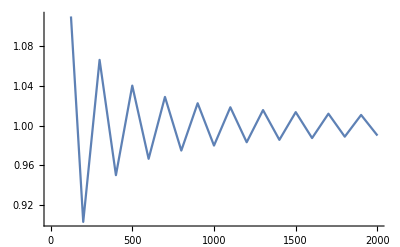

```mathematica
ListPlot[Table[{n,jf[n,0.99]},{n,100,2000,100}],Joined->True]
```

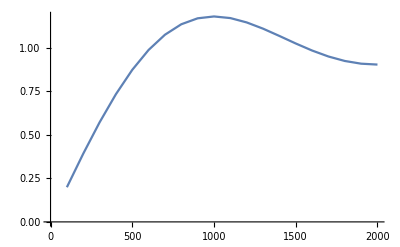

```mathematica
ListPlot[Table[{n,jf[n,0.999]},{n,100,2000,100}],Joined->True]
```

### 3.

This command evaluates the sum of the first 10*2^n terms in the given series.

```mathematica
Table[ NSum[1/(2k-1),{k,1,10*2^n}],{n,0,10}]
```

{2.13326,2.47967,2.82621,3.17277,3.51934,3.86592,4.21249,4.55906,4.90564,5.25221,5.59878}

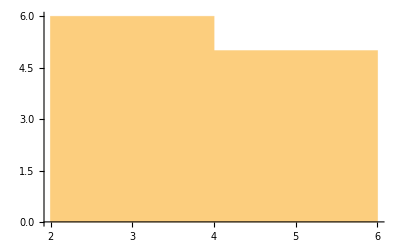

```mathematica
Histogram[{2.133255530159555,2.479673210364535,2.826207759335609,3.1727715853245346,3.519342734281693,3.8659157142153258,4.212489151907722,4.559062704040743,4.905636284783974,5.25220987267977,5.598783462364047}]
```

### 4.

We denote the sum of the first n terms of this series as

```mathematica
z[n_,x_,w_]:=N[4 Sum[(-1)^((i-1)/2) Exp[-i Pi w/2] Cos[i Pi x/2]/i,{i,1,2n-1,2}]/Pi]
```

and then do a 3-dimensional plot using

```mathematica
Animate[Plot3D[z[n,x,w],{x,-1,1},{w,0,0.6},PlotRange->All],{n,1,20}]
```

### 5.

The following command will compute the first n terms of the series

```mathematica
s[n_]:=NSum[(-1)^(Floor[(k-1)/2]) /(6*Floor[k/2]+(-1)^(k-1)),{k,1,n}]
```

```mathematica
Table[s[n],{n,1,20}]
```

### 7.

The following command will compute the first n terms of the series

```mathematica
g[n_,x_]:=N[2 Sum[(-1)^i Sin[(2i-1) Pi x/2],{i,1,n}]]
```

```mathematica
Animate[Plot[g[n,x],{x,-1,3}],{n,10,50,1}]
```

```mathematica
Table[g[n,0],{n,1,20}]
```

```mathematica
Table[g[n,.2],{n,1,20}]
```

```mathematica
Table[g[n,.3],{n,1,20}]
```

```mathematica
Table[g[n,.5],{n,1,20}]
```